```mathematica
ClearGlobal[]:=(ClearAll["Global`*"];Clear[Derivative];);
```

```mathematica
ClearGlobal[]
```

```mathematica
RemoveGlobal[]:=(ClearGlobal[];Remove["Global`*"];);
```

```mathematica
RemoveGlobal[]
```

```mathematica
Costly ornaments in sexual selection
```

Reproducing Seger (1985) paper  on sexual selection

## Basic Model

```mathematica
Subscript[U, 2] := Subscript[a, 2]*Subscript[t', 2]/(Subscript[t', 1]+Subscript[a, 2]*Subscript[t', 2])
```

```mathematica
Subscript[U, 2]
```

(a_2 t'_2)/(t'_1+a_2 t'_2)

```mathematica
Subscript[U, 1] := Subscript[t', 1]/(Subscript[t', 1]+Subscript[a, 2]*Subscript[t', 2])
```

```mathematica
Subscript[U, 1]
```

t'_1/(t'_1+a_2 t'_2)

```mathematica
Subscript[V, 2] :=Subscript[t', 2]*Subscript[p, 1]+Subscript[U, 2]*Subscript[p, 2]
```

```mathematica
Subscript[V, 1] :=Subscript[t', 1]*Subscript[p, 1]+Subscript[U, 1]*Subscript[p, 2]
```

```mathematica
Subscript[W, 2] := Subscript[V, 2] / Subscript[t, 2]
```

```mathematica
Subscript[W, 1] := Subscript[V, 1] / Subscript[t, 1]
```

```mathematica
Subscript[t, 1] := 1 - Subscript[t, 2]
```

```mathematica
Subscript[p, 1] := 1- Subscript[p, 2]
```

```mathematica
M := 1 - s * Subscript[t, 2]
```

```mathematica
Subscript[t', 2] := (1-s) * Subscript[t, 2] / M
```

```mathematica
Subscript[t', 1] := Subscript[t, 1] / M
```

```mathematica
sol:= Simplify[Solve[Subscript[W, 1]==Subscript[W, 2], Subscript[p, 2]]]
```

```mathematica
sol
```

{{p_2→(s (-1+(1+(-1+s) a_2) t_2))/((-1+s) (-1+a_2))}}

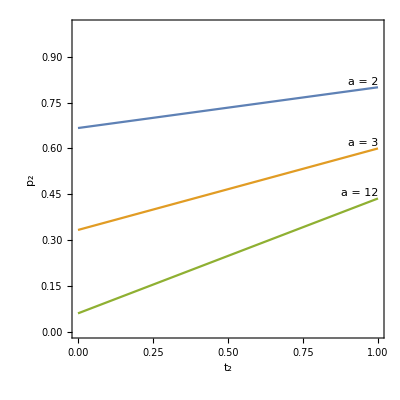

```mathematica
fig1a = Plot[Evaluate[Subscript[p,2]/.sol /. {s -> 0.4, Subscript[a, 2] -> {2, 3, 12}}], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},  FrameLabel->{Defer[Subscript[t, 2]], Defer[Subscript[p, 2]]},AspectRatio->1,Frame->True,PlotLabels->Placed[{"a = 2", "a = 3", "a = 12"},{Scaled[1]}],BaseStyle->{FontSize->12}]
```

```mathematica
W2line := Subscript[W, 2]/.s->0.4/.Subscript[a, 2]->3/.Subscript[p, 2]->0.5
```

```mathematica
W1line := Subscript[W, 1]/.s->0.4/.Subscript[a, 2]->3/.Subscript[p, 2]->0.5
```

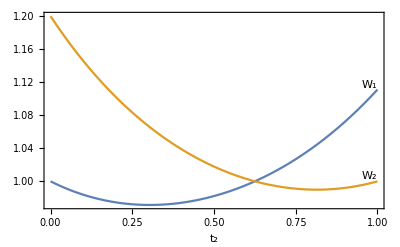

```mathematica
fig1b = Plot[{W1line, W2line}, {Subscript[t, 2], 0, 1}, Frame->True,FrameLabel->Automatic, PlotLabels->Placed[{Defer[Subscript[W, 1]], Defer[Subscript[W, 2]]}, {Scaled[1]}],BaseStyle->{FontSize->12}]
```

## Best of N case

```mathematica
Subscript[U', 2] := Subscript[t', 2] + c Subscript[t', 1]Subscript[t', 2]
```

```mathematica
Subscript[U', 1] := Subscript[t', 1] - c Subscript[t', 1]Subscript[t', 2]
```

```mathematica
Subscript[V', 2] :=Subscript[t', 2]*Subscript[p, 1]+Subscript[U', 2]*Subscript[p, 2]
```

```mathematica
Subscript[V', 1] :=Subscript[t', 1]*Subscript[p, 1]+Subscript[U', 1]*Subscript[p, 2]
```

```mathematica
Subscript[W', 2] := Subscript[V', 2] / Subscript[t, 2]
```

```mathematica
Subscript[W', 1] := Subscript[V', 1] / Subscript[t, 1]
```

```mathematica
sol':= Simplify[Solve[Subscript[W', 1]==Subscript[W', 2], Subscript[p, 2]]]
```

```mathematica
sol'
```

{{p_2→(s (-1+s t_2))/(c (-1+s))}}

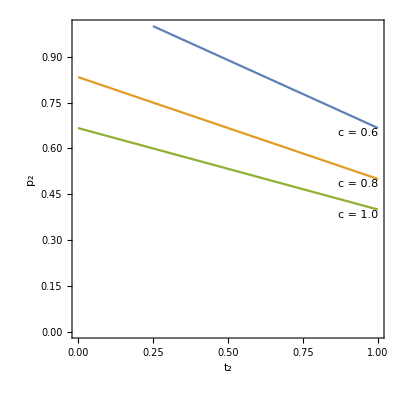

```mathematica
fig2a = Plot[Evaluate[Subscript[p,2]/.sol' /. {s -> 0.4, c -> {0.6, 0.8, 1.0}}], {Subscript[t, 2], 0, 1}, PlotRange->{0,1}, FrameLabel->{Defer[Subscript[t, 2]], Defer[Subscript[p, 2]]},AspectRatio->1,Frame->True, PlotLabels->Placed[{"c = 0.6", "c = 0.8", "c = 1.0"},{Scaled[1]}],BaseStyle->{FontSize->12}]
```

```mathematica
px2:=Subscript[W', 2]/.s->0.4/.c->1/.Subscript[p, 2]->0.5
```

```mathematica
px1:= Subscript[W',1]/.s->0.4/.c->1/.Subscript[p, 2]->0.5
```

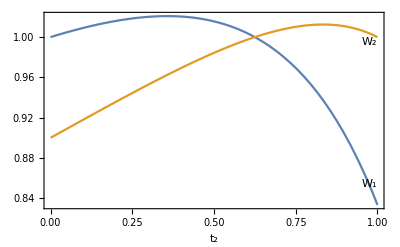

```mathematica
fig2b = Plot[{px1, px2}, {Subscript[t, 2], 0, 1}, FrameLabel->Automatic, Frame->True,PlotLabels->Placed[{Defer[Subscript[W, 1]], Defer[Subscript[W, 2]]},{Scaled[1]}],BaseStyle->{FontSize->12}]
```

```mathematica
eq1 := Plot[Evaluate[Subscript[p,2]/.sol /. {s -> 0.4, Subscript[a, 2] -> 3}], {Subscript[t, 2], 0, 1}, PlotRange->{0,1},  PlotStyle->Black,FrameLabel->{Defer[Subscript[t, 2]], Defer[Subscript[p, 2]]},AspectRatio->1,Frame->True]
```

```mathematica
eq2 := Plot[Evaluate[Subscript[p,2]/.sol' /. {s -> 0.4, c ->  1.0}], {Subscript[t, 2], 0, 1}, PlotRange->{0,1}, PlotStyle->Black, FrameLabel->{Defer[Subscript[t, 2]], Defer[Subscript[p, 2]]},AspectRatio->1,Frame->True]
```

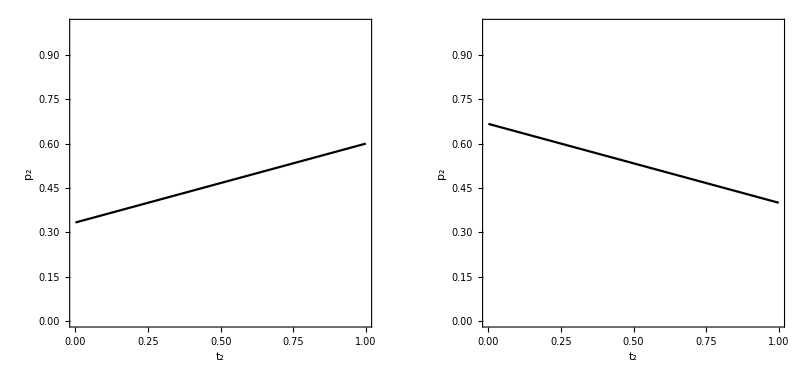

```mathematica
GraphicsRow[{eq1, eq2}]
```

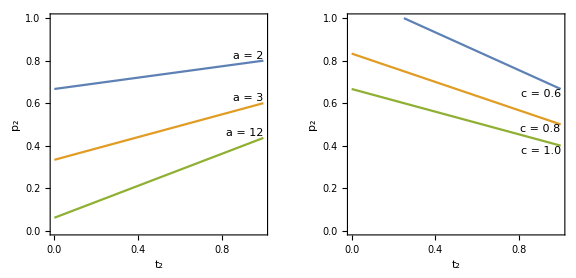

```mathematica
GraphicsRow[{fig1a, fig2a}, ImageSize->Large]
```

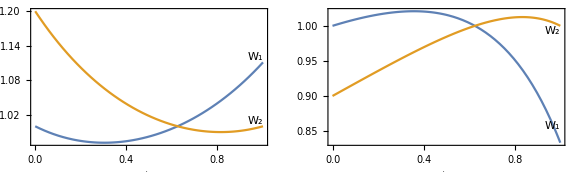

```mathematica
GraphicsRow[{fig1b, fig2b}, ImageSize->Large]
```

```mathematica
contourDensityPlot[f_,rx_,ry_,opts:OptionsPattern[]]:=(* //Created by Jens U.Nöckel for Mathematica 8,revised 12/2011*)Module[{img,cont,pL,p,plotRangeRule,densityOptions,contourOptions,frameOptions,rangeCoords},densityOptions=Join[FilterRules[{opts},FilterRules[Options[DensityPlot],Except[{ImageSize,Prolog,Epilog,FrameTicks,PlotLabel,ImagePadding,GridLines,Mesh,AspectRatio,PlotRangePadding,Frame,Axes}]]],{PlotRangePadding->None,ImagePadding->None,Frame->None,Axes->None}];
pL=DensityPlot[f,rx,ry,Evaluate@Apply[Sequence,densityOptions]];
p=First@Cases[{pL},Graphics[__],∞];
plotRangeRule=FilterRules[Quiet@AbsoluteOptions[p],PlotRange];
contourOptions=Join[FilterRules[{opts},FilterRules[Options[ContourPlot],Except[{Prolog,Epilog,FrameTicks,Background,ContourShading,Frame,Axes}]]],{Frame->None,Axes->None,ContourShading->False}];
(* //The density plot img and contour plot cont are created here:*)img=Rasterize[p,"Image"];
cont=If[MemberQ[{0,None},(Contours/.FilterRules[{opts},Contours])],{},ContourPlot[f,rx,ry,Evaluate@Apply[Sequence,contourOptions]]];
(* //Before showing the plots,set the PlotRange for the frame which will be drawn separately:*)frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
(* //To align the image img with the contour plot,enclose img in a//bounding box rectangle of the same dimensions as cont,
//and then combine with cont using Show:*)If[Head[pL]===Legended,Legended[#,pL[[2]]],#]&@Show[Graphics[{Inset[Show[SetAlphaChannel[img,"ShadingOpacity"/.{opts}/.{"ShadingOpacity"->1}],AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]},PlotRangePadding->None],cont,Evaluate@Apply[Sequence,frameOptions]]]
```

```mathematica
fig1a'' :=  contourDensityPlot[Log[Subscript[W, 2]/Subscript[W, 1]]/. s-> 0.4/. Subscript[a, 2]->3,{Subscript[t, 2],0,1},{Subscript[p, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][(#1 + 1)/2]&),ColorFunctionScaling->False,FrameLabel->{Defer[Subscript[p, 2]],Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]
```

```mathematica
fig2a'':=contourDensityPlot[Log[Subscript[W', 2]/Subscript[W', 1]]/. s-> 0.4/. c->1,{Subscript[t, 2],0,1},{Subscript[p, 2],0,1},  ColorFunction->(ColorData["ThermometerColors"][(#1 + 1)/2]&),ColorFunctionScaling->False,FrameLabel->{Defer[Subscript[p, 2]],Defer[Subscript[t, 2]]},BaseStyle->{FontSize->12}]
```

```mathematica
GraphicsRow[{Show[fig1a'', eq1], Show[fig2a'', eq2]}, ImageSize->Large]
```